```mathematica
u2[x_,L_,U_,w_]:=Piecewise[{{2*((x-L)/w)^3-3*((x-L)/w)^2+1,x >L && x <L+w},{0, x > L+w && x < U-w}, {2*((U-x)/w)^3-3*((U-x)/w)^2+1,x > U-w && x < U}, {1, x< L || x > U}}]
```

```mathematica
u1[x_]:=Piecewise[{{2*x^3 - 3*x^2 + 1,x > 0 && x < 1},{0 ,x > 1}, {1, x <0}}]
```

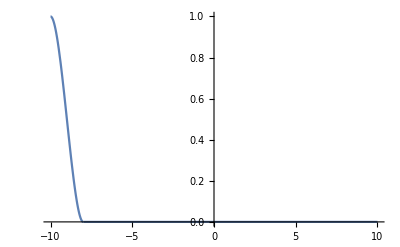

```mathematica
Plot[u1[(x+10)/2], {x,-10,10}]
```

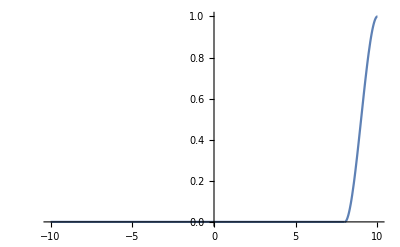

```mathematica
Plot[u1[(10-x)/2], {x,-10,10}]
```

```mathematica
g[x_,s_,L_,U_,w_,b_]:= E^(-(x-s)^2/w^2) + (E^(-(x - L)^2/w^2) - E^(-(x-s)^2/w^2))*u1[(s - L)/(b*w)] + (E^(-(x-U)^2/w^2) - E^(-(x-s)^2/w^2))*u1[(U-s)/(b*w)]
```

```mathematica
Animate[Plot[g[x,s,-10,10,2,1], {s,-10,10},PlotRange->{0,1}],{x,-10,10}]
```

```mathematica
Animate[Plot[D[g[x,ds,-10,10,2,1],ds] /.{ds->s}, {s,-10,10},PlotRange->{0,1}],{x,-10,10}]
```

```mathematica
Int3 =Integrate[g[x,s,L,U,w,b],{x,L,U}]
```

1/2 w (-1.77245 Erf[(L-s)/w]-1.77245 Erf[(s-U)/w]+(1.77245 Erf[(L-s)/w]-0.443113 Erf[(L-U)/w]+1.77245 Erf[(s-U)/w]) (Piecewise[{{((L-s+b w)^2 (-2 L+2 s+b w))/(b^3 w^3), b L w<b s w&&b w (L-s+b w)>0}, {0, b w (L-s+b w)<0||(-L+s)/(b w)≥0}, {1, True}}])+(1.77245 Erf[(L-s)/w]-0.443113 Erf[(L-U)/w]+1.77245 Erf[(s-U)/w]) (Piecewise[{{((s-U+b w)^2 (-2 s+2 U+b w))/(b^3 w^3), b s w<b U w&&b w (s-U+b w)>0}, {0, b w (s-U+b w)<0||(-s+U)/(b w)≥0}, {1, True}}]))

```mathematica
gbar[s1_,L1_,U1_,w1_,b1_]:= Int3/.{s->s1,L->L1,U->U1,w->w1,b->b1}
```

```mathematica
gbar[0,-10,10,1,1]
```

1.77245

```mathematica
gcorrected[x_,s_,L_,U_,w_,b_]:=g[x,s,L,U,w,b] / gbar[s,L,U,w,b]
```

```mathematica
gcorrected[x,s,L,U,w,b]
```

(2 (ⅇ^(-(-s+x)^2/w^2)+(0.25 ⅇ^(-(-L+x)^2/w^2)-ⅇ^(-(-s+x)^2/w^2)) (Piecewise[{{1+(2 (-L+s)^3)/(b^3 w^3)-(3 (-L+s)^2)/(b^2 w^2), (-L+s)/(b w)>0&&(-L+s)/(b w)<1}, {0, (-L+s)/(b w)>1}, {1, (-L+s)/(b w)<0}, {0, True}}])+(-ⅇ^(-(-s+x)^2/w^2)+0.25 ⅇ^(-(-U+x)^2/w^2)) (Piecewise[{{1+(2 (-s+U)^3)/(b^3 w^3)-(3 (-s+U)^2)/(b^2 w^2), (-s+U)/(b w)>0&&(-s+U)/(b w)<1}, {0, (-s+U)/(b w)>1}, {1, (-s+U)/(b w)<0}, {0, True}}])))/(w (-1.77245 Erf[(L-s)/w]-1.77245 Erf[(s-U)/w]+(1.77245 Erf[(L-s)/w]-0.443113 Erf[(L-U)/w]+1.77245 Erf[(s-U)/w]) (Piecewise[{{((L-s+b w)^2 (-2 L+2 s+b w))/(b^3 w^3), b L w<b s w&&b w (L-s+b w)>0}, {0, b w (L-s+b w)<0||(-L+s)/(b w)≥0}, {1, True}}])+(1.77245 Erf[(L-s)/w]-0.443113 Erf[(L-U)/w]+1.77245 Erf[(s-U)/w]) (Piecewise[{{((s-U+b w)^2 (-2 s+2 U+b w))/(b^3 w^3), b s w<b U w&&b w (s-U+b w)>0}, {0, b w (s-U+b w)<0||(-s+U)/(b w)≥0}, {1, True}}])))

```mathematica
Animate[Plot[{gcorrected[x,s,-10,10,2,3],E^(-(x-s)^2/4)/(0.5*Sqrt[Pi]*2*(Erf[(s+10)/2] + Erf[(10-s)/2]))}, {s,-10,10},PlotRange->{0,1}],{x,-10,10}]
```

```mathematica
Animate[Plot[{D[gcorrected[x,ds,-10,10,2,3],ds]/.{ds->s},D[E^(-(x-ds)^2/4)/(0.5*Sqrt[Pi]*2*(Erf[(ds+10)/2] + Erf[(10-ds)/2])),ds]/.{ds->s}}, {s,-10,10},PlotRange->{0,1}],{x,-10,10}]
```

```mathematica
dgs[x_,s_,U_,L_,w_,b_]:=D[gcorrected[x,ds,U,L,w,b], ds]/.{ds->s}
```

```mathematica
dgs[1,4,-10,10,1,1]
```

-(2 (2/(ⅇ^196 √π)-2/(ⅇ^36 √π)))/(ⅇ^9 √π (-2+Erfc[-14]+Erfc[-6])^2)-12/(ⅇ^9 √π (-2+Erfc[-14]+Erfc[-6]))

```mathematica
Integrate[E^(-(x-L)^2/(w^2)), {x,L,Infinity}]
```

ConditionalExpression[(√π)/(2 √(1/w^2)),(Re[1/w^2]≥0&&Re[L/w^2]<0)||Re[1/w^2]>0]

```mathematica
Integrate[E^(-(x-s)^2/(w^2)), {x,L,U}]
```

-1/2 √π w (Erf[(L-s)/w]+Erf[(s-U)/w])

```mathematica
D[Integrate[E^(-(x-s)^2/(w^2)), {x,L,U}],s]
```

-1/2 √π (-(2 ⅇ^(-(L-s)^2/w^2))/(√π w)+(2 ⅇ^(-(s-U)^2/w^2))/(√π w)) w

```mathematica
Integrate[E^(-(x-s)^2/(w^2)), {x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√(1/w^2)),Re[1/w^2]≥0]

```mathematica
D[E^(-(x-s)^2/(w^2)),s]
```

(2 ⅇ^(-(-s+x)^2/w^2) (-s+x))/w^2